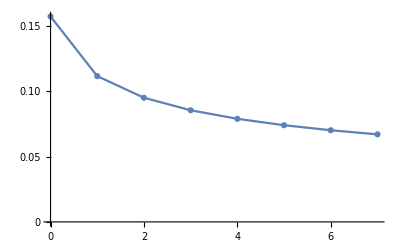

```mathematica
Get["MaTeX`"]
P[v_]:=1/(Sqrt[Pi] 2^(v-1) v!)NIntegrate[(HermiteH[v,y])^2 E^(-y^2),{y,Sqrt[2 v+1],+Infinity}]

ListLinePlot[Table[{v,P[v]},{v,0,7}],
PlotMarkers->Automatic,
PlotRange->{{0,7},All},
Ticks->{Table[{i,i},{i,0,7}],All},
AxesLabel->{MaTeX["v"],MaTeX["P_v"]},
LabelStyle->Directive[FontFamily->"CMU Serif",FontSize->10.5]
]
```